```mathematica
Clear[x,y];
d = 1;
r = 1;
mse[g_,r_]:= Total[(g-r)^2];
Plot3D[{mse[{g},{r}]},{g,-d,d},{r,-d,d},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(** Mean absolute error **)
mae[x_,y_]:=Total[Abs[(x-y)]];
Plot3D[{mae[{x},{y}]},{x,-d,d},{y,-d,d},AxesLabel->Automatic]
```

-Graphics3D-

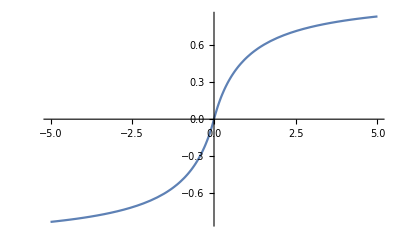

-Graphics3D-

```mathematica
softsign[x_]:=x/(1+Abs[x]);
Plot[softsign[x], {x,-5,5}]
msedir[x_,y_] := mae[softsign[x],softsign[y]];
Plot3D[msedir[{x},{y}],{x,-r,r},{y,-r,r},AxesLabel->Automatic]
```

```mathematica
Plot3D[{mse[{x},{y}],mae[{x},{y}], msedir[{x},{y}]},{x,-r,r},{y,-r,r},AxesLabel->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
l2_norm[x_]:=x/Norm[{x}];
cs[x_,y_]:=1-x/Norm[{x}]*y/Norm[{y}];
Plot3D[cs[{x},{y}],{x,-r,r},{y,-r,r},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
logcos[x_,y_]:=Log[(Exp[x-y]+Exp[-x+y])/2]
Plot3D[{mse[{x},{y}],logcos[x,y]},{x,-r,r},{y,-r,r},AxesLabel->Automatic, PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
poisson[x_,y_]:=x-y*Log[x];
Plot3D[poisson[{x},{y}],{x,0,1},{y,0,1},AxesLabel->Automatic, PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
msess[x_,y_] :=mae[x,y]*(1+mae[softsign[x],softsign[y]]);
Plot3D[msess[{x},{y}],{x,-r,r},{y,-r,r},AxesLabel->Automatic]
```

-Graphics3D-